## Solutions: Mathematica 6 Lab 5

Problem 1: Invaded Planetary System

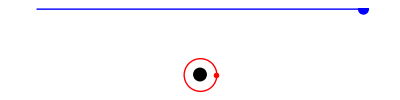

```mathematica
Show[Graphics[{
{AbsolutePointSize[10],Point[{0,0}]},
{Red,Circle[{0,0},1]},
{Red,AbsolutePointSize[4],Point[{1,0}]},
{Blue,Line[{{-10,4},{10,4}}]},
{Blue,AbsolutePointSize[8],Point[{10,4}]}
}],AspectRatio->Automatic]
```

```mathematica
UnperturbedOrbit=NDSolve[{x''[t]==-(9x[t])/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-(9y[t])/((x[t]^2+y[t]^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==3},{x[t],y[t]},{t,0,3}]
```

{{x[t]→InterpolatingFunction[{{0.,3.}},<>][t],y[t]→InterpolatingFunction[{{0.,3.}},<>][t]}}

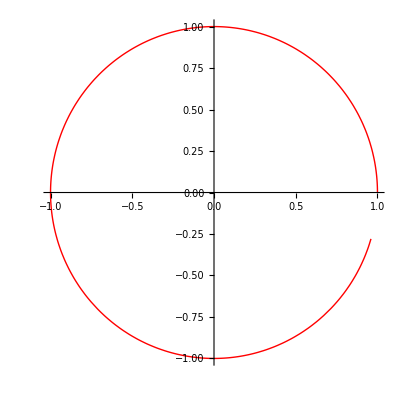

```mathematica
ShowUnperturbed=ParametricPlot[Evaluate[{x[t],y[t]}/.UnperturbedOrbit],{t,0,2},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Red]
```

```mathematica
PerturbedOrbit=NDSolve[{x''[t]==-(9x[t])/((x[t]^2+y[t]^2)^(3/2))+(1/2(10-x[t]))/(((10-x[t])^2+(4-y[t])^2)^(3/2)),
y''[t]==-(9y[t])/((x[t]^2+y[t]^2)^(3/2))+(1/2(4-y[t]))/(((10-x[t])^2+(4-y[t])^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==3},{x[t],y[t]},{t,0,80}]
```

{{x[t]→InterpolatingFunction[{{0.,80.}},<>][t],y[t]→InterpolatingFunction[{{0.,80.}},<>][t]}}

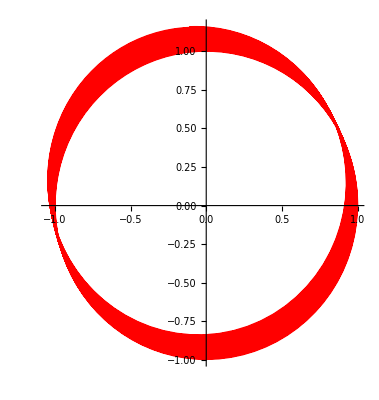

```mathematica
ShowPerturbed=ParametricPlot[Evaluate[{x[t],y[t]}/.PerturbedOrbit],{t,0,80},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Red]
```

```mathematica
ImpactedOrbit=NDSolve[{x''[t]==-(9x[t])/((x[t]^2+y[t]^2)^(3/2))+(1/2(10-t/4-x[t]))/(((10-t/4-x[t])^2+(4-y[t])^2)^(3/2)),
y''[t]==-(9y[t])/((x[t]^2+y[t]^2)^(3/2))+(1/2(4-y[t]))/(((10-t/4-x[t])^2+(4-y[t])^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==3},{x[t],y[t]},{t,0,80}]
```

{{x[t]→InterpolatingFunction[{{0.,80.}},<>][t],y[t]→InterpolatingFunction[{{0.,80.}},<>][t]}}

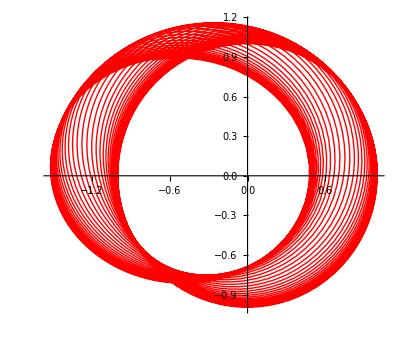

```mathematica
ShowImpacted=ParametricPlot[Evaluate[{x[t],y[t]}/.ImpactedOrbit],{t,0,80},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Red]
```

```mathematica
ReverseImpact=NDSolve[{x''[t]==-(9x[t])/((x[t]^2+y[t]^2)^(3/2))+(1/2(-10+t/4-x[t]))/(((-10+t/4-x[t])^2+(4-y[t])^2)^(3/2)),
y''[t]==-(9y[t])/((x[t]^2+y[t]^2)^(3/2))+(1/2(4-y[t]))/(((-10+t/4-x[t])^2+(4-y[t])^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==3},{x[t],y[t]},{t,0,80}]
```

{{x[t]→InterpolatingFunction[{{0.,80.}},<>][t],y[t]→InterpolatingFunction[{{0.,80.}},<>][t]}}

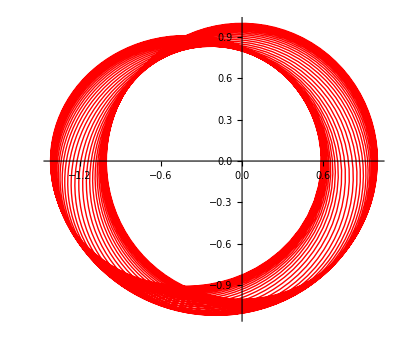

```mathematica
ShowReverse=ParametricPlot[Evaluate[{x[t],y[t]}/.ReverseImpact],{t,0,80},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Red]
```

Problem 2:

```mathematica
Hyperlink["Van der Pol","http://www.scholarpedia.org/article/Van_der_Pol_Oscillator"]
```

```mathematica
Clear[b,x,μ,t]
```

```mathematica
b[x_,μ_]:=μ(x^2-1)
```

```mathematica
solv1=NDSolve[{x''[t]+b[x[t],1/8]x'[t]+x[t]==0,x[0]==1,x'[0]==0},x[t],{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

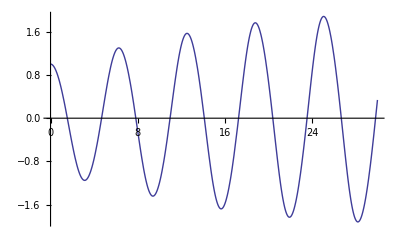

```mathematica
graph1=Plot[x[t]/.solv1,{t,0,30}]
```

```mathematica
solv2=NDSolve[{x''[t]+b[x[t],1/8]x'[t]+x[t]==0,x[0]==4,x'[0]==0},x[t],{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

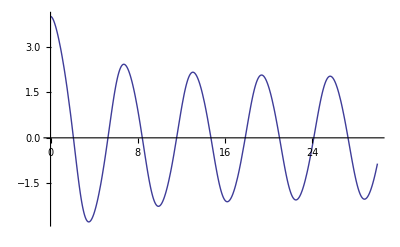

```mathematica
graph2=Plot[x[t]/.solv2,{t,0,30}]
```

```mathematica
solv3=NDSolve[{x''[t]+b[x[t],8]x'[t]+x[t]==0,x[0]==1,x'[0]==0},x[t],{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

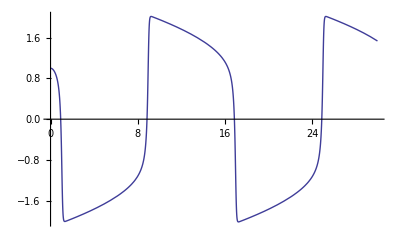

```mathematica
graph3=Plot[x[t]/.solv3,{t,0,30}]
```

```mathematica
phase1=NDSolve[{x'[t]==y[t],y'[t]+8(x[t]^2-1)y[t]+x[t]==0,x[0]==0,y[0]==1},{x[t],y[t]},{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t],y[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

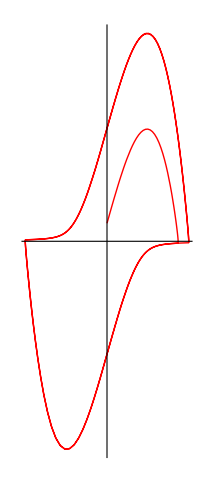

```mathematica
phasemap1=ParametricPlot[{x[t],y[t]}/.phase1,{t,0,30},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Red,Ticks->None]
```

```mathematica
phase2=NDSolve[{x'[t]==y[t],y'[t]+8(x[t]^2-1)y[t]+x[t]==0,x[0]==0,y[0]==12},{x[t],y[t]},{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t],y[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

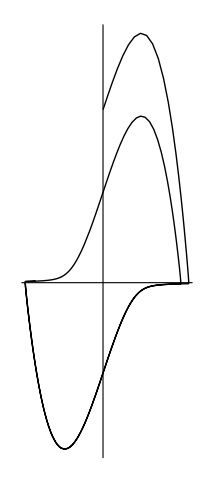

```mathematica
phasemap2=ParametricPlot[{x[t],y[t]}/.phase2,{t,0,30},
PlotRange->All,
 AspectRatio->Automatic,PlotStyle->Black,Ticks->None]
```

```mathematica
phase3=NDSolve[{x'[t]==y[t],y'[t]+8(x[t]^2-1)y[t]+x[t]==0,x[0]==2.1,y[0]==17.2},{x[t],y[t]},{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t],y[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

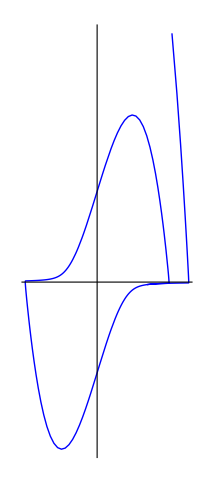

```mathematica
phasemap3=ParametricPlot[{x[t],y[t]}/.phase3,{t,0,30},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Blue,Ticks->None]
```

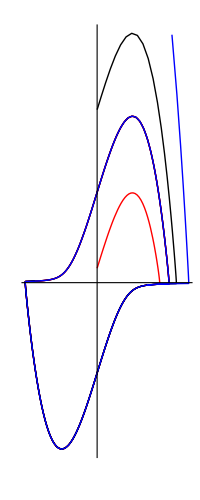

```mathematica
Show[phasemap1, phasemap2, phasemap3]
```

Problem 3: Oscillators, Coupled in Various Ways

```mathematica
Uncoupled=NDSolve[{x''[t]+2^2 x[t]==0,y''[t]+5^2 y[t]==0,x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

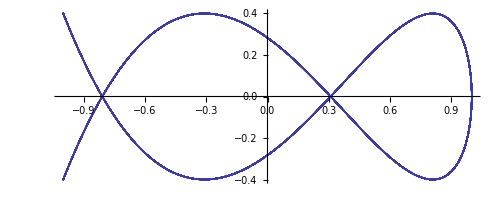

```mathematica
ParametricPlot[{x[t],y[t]}/.Uncoupled,{t,0,100}, AspectRatio->Automatic,PlotRange->{{-1,1},{-.4,.4}}]
```

```mathematica
DampedUncoupled=NDSolve[{x''[t]+2^2 x[t]==-.1x'[t],y''[t]+5^2 y[t]==-.1y'[t],x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

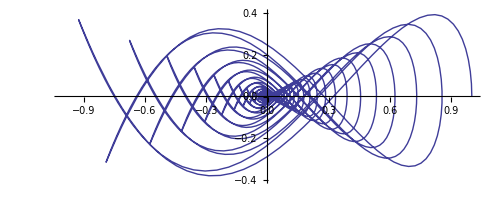

```mathematica
ParametricPlot[{x[t],y[t]}/.DampedUncoupled,{t,0,100}, AspectRatio->Automatic,PlotRange->{{-1,1},{-.4,.4}}]
```

```mathematica
UndampedCoupled=NDSolve[{x''[t]+2^2 x[t]==5y[t],y''[t]+5^2 y[t]==5x[t],x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

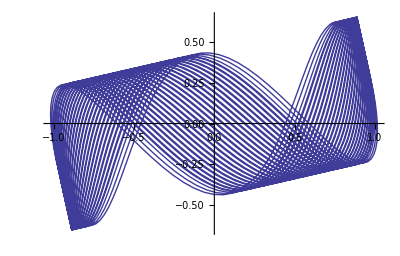

```mathematica
ParametricPlot[{x[t],y[t]}/.UndampedCoupled,{t,0,100}, AspectRatio->Automatic]
```

```mathematica
UndampedCoupled2=NDSolve[{x''[t]+2^2 x[t]==9y[t],y''[t]+5^2 y[t]==9x[t],x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

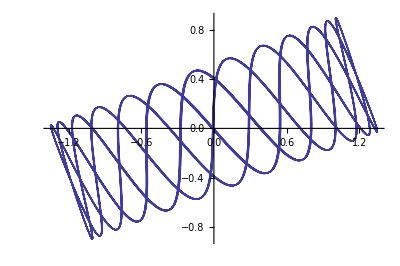

```mathematica
ParametricPlot[{x[t],y[t]}/.UndampedCoupled2,{t,0,100}, AspectRatio->Automatic]
```

```mathematica
UndampedCoupled3=NDSolve[{x''[t]+2^2 x[t]==9.999y[t],y''[t]+5^2 y[t]==9.999x[t],x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

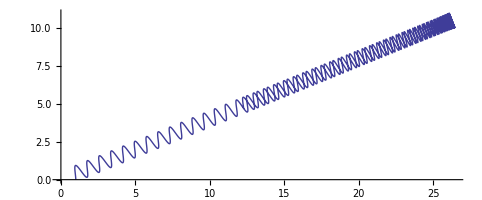

```mathematica
ParametricPlot[{x[t],y[t]}/.UndampedCoupled3,{t,0,100}, AspectRatio->Automatic]
```

```mathematica
DampedCoupled=NDSolve[{x''[t]+2^2 x[t]==-.005x'[t]+9y[t],y''[t]+5^2 y[t]==-.005y'[t]9+x[t],x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

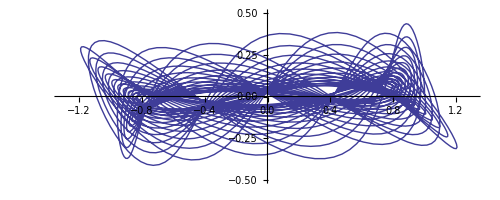

```mathematica
ParametricPlot[{x[t],y[t]}/.DampedCoupled,{t,0,100}, AspectRatio->Automatic, PlotRange->{{-1.3,1.3},{-.5,.5}}]
```

```mathematica
GyroCoupled=NDSolve[{x''[t]+2y'[t]+2^2 x[t]==0,y''[t]-2x'[t]+5^2 y[t]==0,x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

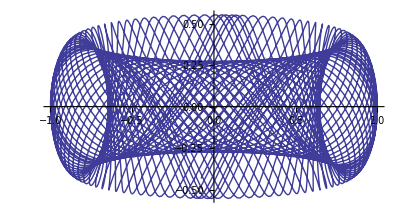

```mathematica
ParametricPlot[{x[t],y[t]}/.GyroCoupled,{t,0,100}, AspectRatio->Automatic]
```

```mathematica
HybridCoupled=NDSolve[{x''[t]+.6y'[t]+2^2 x[t]==0,y''[t]-.6x[t]+5^2 y[t]==0,x[0]==1,y[0]==0,x'[0]==0,y'[0]==2},{x[t],y[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[{{0.,100.}},<>][t],y[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

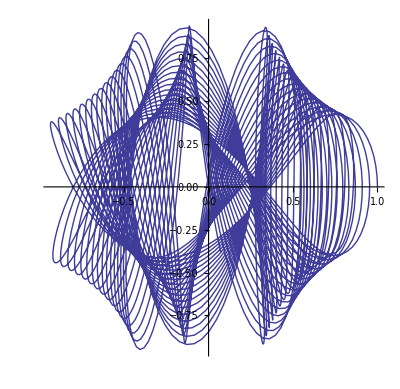

```mathematica
ParametricPlot[{x[t],y[t]}/.HybridCoupled,{t,0,100}, AspectRatio->Automatic]
```